We parameterize a distribution over two discrete actions with a single variable using sigmoids.
This allows us to represent a mixed strategy of two discrete actions as a single continuous variable.

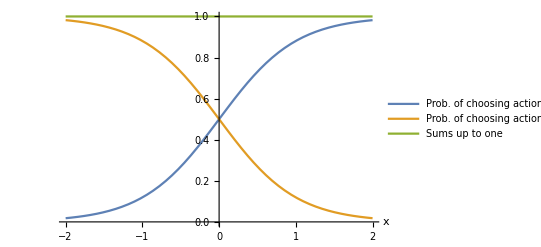

```mathematica
Plot[{Exp[x]/(Exp[x]+Exp[-x]),Exp[-x]/(Exp[x]+Exp[-x]),(Exp[x]+Exp[- x])/(Exp[x]+Exp[-x])},{x,-2,2},PlotLegends->{"Prob. of choosing action 1","Prob. of choosing action 2","Sums up to one"},AxesLabel->{x}]
```

We allow an affine shift in the choice variable for numerical purposes.

```mathematica
pi[x_] ={Exp[a1 x+b1],Exp[a2 x+b2]}/(Exp[a1 x+b1]+Exp[a2 x+b2]);
Plot[pi[x]~Join~Dpi/.{a1->10,a2->-1,b1->0,b2->-2},{x,-1,1}];
```

```mathematica
Dpi={a1-a2,a2-a1}(1-pi[x])pi[x]//Simplify
```

{((a1-a2) ⅇ^(b1+b2+(a1+a2) x))/((ⅇ^(b1+a1 x)+ⅇ^(b2+a2 x))^2),((-a1+a2) ⅇ^(b1+b2+(a1+a2) x))/((ⅇ^(b1+a1 x)+ⅇ^(b2+a2 x))^2)}

```mathematica
D[pi[x],x]-Dpi//Simplify
```

{0,0}

```mathematica
D[D[pi[x],x],x]//Simplify
```

{((a1-a2)^2 ⅇ^(b1+b2+(a1+a2) x) (-ⅇ^(b1+a1 x)+ⅇ^(b2+a2 x)))/((ⅇ^(b1+a1 x)+ⅇ^(b2+a2 x))^3),-((a1-a2)^2 ⅇ^(b1+b2+(a1+a2) x) (-ⅇ^(b1+a1 x)+ⅇ^(b2+a2 x)))/((ⅇ^(b1+a1 x)+ⅇ^(b2+a2 x))^3)}

```mathematica
DDpi=D[D[pi[x],x],x]//Simplify
```

{((a1-a2)^2 ⅇ^(b1+b2+(a1+a2) x) (-ⅇ^(b1+a1 x)+ⅇ^(b2+a2 x)))/((ⅇ^(b1+a1 x)+ⅇ^(b2+a2 x))^3),-((a1-a2)^2 ⅇ^(b1+b2+(a1+a2) x) (-ⅇ^(b1+a1 x)+ⅇ^(b2+a2 x)))/((ⅇ^(b1+a1 x)+ⅇ^(b2+a2 x))^3)}

```mathematica
{a1-a2,a2-a1}(Dpi-2pi[x] Dpi)//Simplify
```

{((a1-a2)^2 ⅇ^(b1+b2+(a1+a2) x) (-ⅇ^(b1+a1 x)+ⅇ^(b2+a2 x)))/((ⅇ^(b1+a1 x)+ⅇ^(b2+a2 x))^3),((a1-a2)^2 ⅇ^(b1+b2+(a1+a2) x) (ⅇ^(b1+a1 x)-ⅇ^(b2+a2 x)))/((ⅇ^(b1+a1 x)+ⅇ^(b2+a2 x))^3)}

```mathematica
pie=Exp[x]/(Exp[x]+Exp[y])
Dpie=D[pie,x]//Simplify
DDpie=D[D[pie,x],x]//Simplify
```

ⅇ^x/(ⅇ^x+ⅇ^y)

ⅇ^(x+y)/((ⅇ^x+ⅇ^y)^2)

(ⅇ^(x+y) (-ⅇ^x+ⅇ^y))/((ⅇ^x+ⅇ^y)^3)

```mathematica
pie - pie//Simplify
```

0

```mathematica
Dpie - (1-pie) pie//Simplify
```

0

```mathematica
DDpie-(Dpie-2Dpie pie)//Simplify
```

0